```mathematica
(* Journal of the Korean Physical Society (2024) 84:59–66
https://doi.org/10.1007/s40042-023-00979-4 *)
```

## Ham

```mathematica
(* -Graphics- *)
(*** Gell Mann Matrices **)
λ1=({{0, 1, 0}, {1, 0, 0}, {0, 0, 0}});λ2=({{0, -ⅈ, 0}, {ⅈ, 0, 0}, {0, 0, 0}});λ3=({{1, 0, 0}, {0, -1, 0}, {0, 0, 0}});λ4=({{0, 0, 1}, {0, 0, 0}, {1, 0, 0}});
λ5=({{0, 0, -ⅈ}, {0, 0, 0}, {ⅈ, 0, 0}});λ6=({{0, 0, 0}, {0, 0, 1}, {0, 1, 0}});λ7=({{0, 0, 0}, {0, 0, -ⅈ}, {0, ⅈ, 0}});λ8=1/(√3)({{1, 0, 0}, {0, 1, 0}, {0, 0, -2}});
(**** Spin-1 rotation operators ****)
Sx=({{0, 1/(√2), 0}, {1/(√2), 0, 1/(√2)}, {0, 1/(√2), 0}});Sy=1/(√2)({{0, -ⅈ, 0}, {ⅈ, 0, -ⅈ}, {0, ⅈ, 0}});Sz=({{1, 0, 0}, {0, 0, 0}, {0, 0, -1}});
√2 Sx==λ1+λ6//FullSimplify
√2 Sy==λ2+λ7//FullSimplify
2Sz==λ3+√3 λ8
(****** 3-band Berrry-dipole node *******)
h3=kx λ1+ky λ2+kz λ5;
FullSimplify[Eigenvalues[h3]/.rep,ass]
```

True

True

True

{0,-k,k}

```mathematica
M=(A0+ⅈ B0)IdentityMatrix[3]+(A1+ⅈ B1)λ1+(A2+ⅈ B2)λ2+(A3+ⅈ B3)λ3+(A4+ⅈ B4)λ4+(A5+ⅈ B5)λ5+(A6+ⅈ B6)λ6+(A7+ⅈ B7)λ7+(A8+ⅈ B8)λ8;
Mdag=(A0-ⅈ B0)IdentityMatrix[3]+(A1-ⅈ B1)λ1+(A2-ⅈ B2)λ2+(A3-ⅈ B3)λ3+(A4-ⅈ B4)λ4+(A5-ⅈ B5)λ5+(A6-ⅈ B6)λ6+(A7-ⅈ B7)λ7+(A8-ⅈ B8)λ8;
eqs=Mdag.λ5+λ5.M//FullSimplify;
eqs//MatrixForm
Reduce[eqs[[1,1]]==0 && eqs[[1,2]]==0 && eqs[[1,3]]==0 && eqs[[2,1]]==0 &&  eqs[[2,3]]==0 && eqs[[3,1]]==0 && eqs[[3,2]]==0&& eqs[[3,3]]==0,{A0,B1,A3,B2,A5,B3,A8,B4}(*{A1,A2,A3,A4,A5,A6,A7,A8,A9}*) ]
```

(2 (A5+B4) | -ⅈ A6+A7+B6+ⅈ B7 | -2 ⅈ A0-ⅈ A3+(ⅈ A8)/(√3)-B3-√3 B8
ⅈ A6+A7+B6-ⅈ B7 | 0 | -ⅈ A1+A2-B1-ⅈ B2
2 ⅈ A0+ⅈ A3-(ⅈ A8)/(√3)-B3-√3 B8 | ⅈ A1+A2-B1+ⅈ B2 | 2 (A5-B4))

A7==-B6&&A6==B7&&B1==A2&&B2==-A1&&A5==0&&B3==-√3 B8&&A8==2 √3 A0+√3 A3&&B4==0

```mathematica
MM=(A0+ⅈ B0)id+(A1+ⅈ B1)l1+(A2+ⅈ B2)l2+(A3+ⅈ B3)l3+(A4+ⅈ B4)l4+(A5+ⅈ B5)l5+(A6+ⅈ B6)l6+(A7+ⅈ B7)l7+(A8+ⅈ B8)l8/.{A7->-B6,A6->B7,A2->B1,B2->-A1,A0->-A3/2+A8/(2 √3),B3->-√3 B8,B4->0,A5->0}//FullSimplify
```

(A1+ⅈ B1) (l1-ⅈ l2)-ⅈ √3 B8 l3+A3 (-id/2+l3)+A4 l4+ⅈ B5 l5+(ⅈ B6+B7) (l6+ⅈ l7)+A8 (id/(2 √3)+l8)+ⅈ (B0 id+B8 l8)

```mathematica
Mnew=M/.{A7->-B6,A6->B7,B1->A2,B2->-A1,A5->0,B3->-√3 B8,A8->2 √3 A0+√3 A3,B4->0}//FullSimplify;
Mnew//MatrixForm
Mev=Eigenvalues[Mnew]//FullSimplify
```

(3 A0+2 A3+ⅈ B0-(2 ⅈ B8)/(√3) | 0 | A4+B5
2 (A1+ⅈ A2) | 3 A0+ⅈ B0+(4 ⅈ B8)/(√3) | 2 (ⅈ B6+B7)
A4-B5 | 0 | -3 A0-2 A3+ⅈ B0-(2 ⅈ B8)/(√3))

{ⅈ B0-√((3 A0+2 A3)^2+(A4-B5) (A4+B5))-(2 ⅈ B8)/(√3),ⅈ B0+√((3 A0+2 A3)^2+(A4-B5) (A4+B5))-(2 ⅈ B8)/(√3),3 A0+ⅈ B0+(4 ⅈ B8)/(√3)}

```mathematica
Mnew/.{B0->0,B8->0}//FullSimplify//MatrixForm
```

(3 A0+2 A3 | 0 | A4+B5
2 (A1+ⅈ A2) | 3 A0 | 2 (ⅈ B6+B7)
A4-B5 | 0 | -3 A0-2 A3)

```mathematica
x=FullSimplify[Mnew/.{A0->1/3,A4->0,A5->0,B0->0,B8->0,B5->0,A1->0,A2->0,B6->0,B7->0}];
x.x//FullSimplify
```

{{(1+2 A3)^2,0,0},{0,1,0},{0,0,(1+2 A3)^2}}

```mathematica
MM/.{B0->0,B8->0,A0->1/3}//FullSimplify
```

(A1+ⅈ B1) (l1-ⅈ l2)+1/3 (id-2 l3)+(A8 l3)/(√3)+A4 l4+ⅈ B5 l5+(ⅈ B6+B7) (l6+ⅈ l7)+A8 l8

```mathematica
M=A0 IdentityMatrix[3]+A1 λ1+A2 λ2+A3 λ3+A4 λ4+A5 λ5+A6 λ6+A7 λ7+A8 λ8;
eqs=M.λ5+λ5.M//FullSimplify;eqs//MatrixForm
Reduce[eqs[[1,1]]==0 && eqs[[1,2]]==0 && eqs[[1,3]]==0 && eqs[[2,1]]==0 &&  eqs[[2,3]]==0 && eqs[[3,2]]==0 ,{A1,A2,A8,A4,A5,A6}]
mat=M/.{A7->0,A1->0,A2->0,A8->2 √3 A0+√3 A3,A5->0,A6->0}//FullSimplify;
mat//MatrixForm
mat.mat//FullSimplify//MatrixForm
```

(2 A5 | -ⅈ A6+A7 | -1/3 ⅈ (6 A0+3 A3-√3 A8)
ⅈ A6+A7 | 0 | -ⅈ A1+A2
1/3 ⅈ (6 A0+3 A3-√3 A8) | ⅈ A1+A2 | 2 A5)

A7==0&&A1==0&&A2==0&&A8==2 √3 A0+√3 A3&&A5==0&&A6==0

(3 A0+2 A3 | 0 | A4
0 | 3 A0 | 0
A4 | 0 | -3 A0-2 A3)

((3 A0+2 A3)^2+A4^2 | 0 | 0
0 | 9 A0^2 | 0
0 | 0 | (3 A0+2 A3)^2+A4^2)

```mathematica
A0=1/3;A4=Cos[θ];A3=1/2 (-1+Sin[θ]);
(3 A0+2 A3)^2+A4^2//FullSimplify
Clear[A0,A4,A3];
```

1

```mathematica
$PrePrint=#/. {Csc[z_]:>1/Defer@Sin[z],Sec[z_]:>1/Defer@Cos[z]}&;rep={kx-> k Sin[θ] Cos[ϕ],ky-> k Sin[θ]Sin[ϕ],kp-> k Sin[θ],kz-> k Cos[θ], ξ^2->1};
ass=Assumptions->{ξ,vz,v,k,kp,θ,ϕ,θp,ϕp,kx,ky,kz,ek}∈ Reals &&  k>0 && kp>0 && ek>0 && v>0 && vz>0;
Ω3=kz{kx/((kx^2+ky^2+kz^2)^2),ky/((kx^2+ky^2+kz^2)^2),kz/((kx^2+ky^2+kz^2)^2)};
```

```mathematica
(*-Graphics-; The sign of 𝜉 indicates whether the dipole points toward upward(+) or downward(−) along z-axis *)
Clear[ξ,ham];
ham=vf({{0, ξ kx+ⅈ ky, -ⅈ kz}, {ξ kx-ⅈ ky, 0, 0}, {ⅈ kz, 0, 0}});
es=FullSimplify[Eigensystem[ham]/. ξ^2->1,ass] 
ξ=1;
es=FullSimplify[es/.rep,ass]/.{-ⅈ Cos[ϕ]-Sin[ϕ]->-ⅈ ⅇ^(-ⅈ ϕ),ⅈ Cos[ϕ]+Sin[ϕ]->ⅈ ⅇ^(-ⅈ ϕ)}
```

{{0,-√(kx^2+ky^2+kz^2) vf,√(kx^2+ky^2+kz^2) vf},{{0,kz/(ky-ⅈ kx ξ),1},{(ⅈ √(kx^2+ky^2+kz^2))/kz,-(ky+ⅈ kx ξ)/kz,1},{-(ⅈ √(kx^2+ky^2+kz^2))/kz,-(ky+ⅈ kx ξ)/kz,1}}}

{{0,-k vf,k vf},{{0,ⅈ ⅇ^(-ⅈ ϕ) Cot[θ],1},{ⅈ/Cos[θ],-ⅈ ⅇ^(-ⅈ ϕ) Tan[θ],1},{-ⅈ/Cos[θ],-ⅈ ⅇ^(-ⅈ ϕ) Tan[θ],1}}}

```mathematica
-ⅈ ⅇ^(-ⅈ ϕ)==-ⅈ Cos[ϕ]-Sin[ϕ]//FullSimplify
```

True

```mathematica
evecs={Sin[θ]{0,ⅈ ⅇ^(-ⅈ ϕ) Cot[θ],1},Cos[θ]/(√2){ⅈ/Cos[θ],-ⅈ ⅇ^(-ⅈ ϕ) Tan[θ],1},Cos[θ]/(√2){-ⅈ/Cos[θ],-ⅈ ⅇ^(-ⅈ ϕ) Tan[θ],1}}
```

{{0,ⅈ ⅇ^(-ⅈ ϕ) Cos[θ],Sin[θ]},{ⅈ/(√2),-(ⅈ ⅇ^(-ⅈ ϕ) Sin[θ])/(√2),Cos[θ]/(√2)},{-ⅈ/(√2),-(ⅈ ⅇ^(-ⅈ ϕ) Sin[θ])/(√2),Cos[θ]/(√2)}}

## matrix overlap

```mathematica
Clear[ek,vec1,vec1dag];
vec1[θ_,ϕ_]=FullSimplify[{-ⅈ/(√2),-(ⅈ ⅇ^(-ⅈ ϕ) Sin[θ])/(√2),Cos[θ]/(√2)}/.rep,ass];
vec1dag[θ_,ϕ_]=FullSimplify[{ⅈ/(√2),(ⅈ ⅇ^(ⅈ ϕ) Sin[θ])/(√2),Cos[θ]/(√2)}/.rep,ass];
FullSimplify[vec1dag[θ,ϕ].vec1[θ,ϕ],ass]
(***********)
vec2[θ_,ϕ_]=FullSimplify[{ⅈ/(√2),-(ⅈ ⅇ^(-ⅈ ϕ) Sin[θ])/(√2),Cos[θ]/(√2)}/.rep,ass];
vec2dag[θ_,ϕ_]=FullSimplify[{-ⅈ/(√2),(ⅈ ⅇ^(ⅈ ϕ) Sin[θ])/(√2),Cos[θ]/(√2)}/.rep,ass];
FullSimplify[vec2dag[θ,ϕ].vec2[θ,ϕ],ass]
(******************)

vec3[θ_,ϕ_]=FullSimplify[{0,ⅈ ⅇ^(-ⅈ ϕ) Cos[θ],Sin[θ]}/.rep,ass];
vec3dag[θ_,ϕ_]=FullSimplify[{0,-ⅈ ⅇ^(ⅈ ϕ) Cos[θ],Sin[θ]}/.rep,ass];
FullSimplify[vec3dag[θ,ϕ].vec3[θ,ϕ],ass]
```

1

1

1

```mathematica
amp=FullSimplify[Integrate[((vec1dag[θ,ϕ].vec1[θp,ϕp])(vec1dag[θp,ϕp].vec1[θ,ϕ]))/(2π),{ϕp,0,2π}],ass]
```

1/8 (3+4 Cos[θ] Cos[θp]+Cos[2 θ] Cos[2 θp])

## Topological quanitites

```mathematica
FullSimplify[Norm[{0,kz,ky+ⅈ kx ξ}],ass]
```

√(kx^2+ky^2+kz^2)

```mathematica
Clear[en, vec, v1,v2,v3, v1c, v2c,v3c, ψ1, ψ1dag, ψ2dag, ψ2,ψ3, ψ3dag,vecdag, derx,dery];
ξ=1; ham=({{0, ξ kx+ⅈ ky, -ⅈ kz}, {ξ kx-ⅈ ky, 0, 0}, {ⅈ kz, 0, 0}});
en=vf{k,-k,0};
vec={vec1[θ,ϕ],vec2[θ,ϕ],vec3[θ,ϕ]};
vecdag={vec1dag[θ,ϕ],vec2dag[θ,ϕ],vec3dag[θ,ϕ]};
{ψ1,ψ2,ψ3}={1/(√2 √(kx^2+ky^2+kz^2)){-ⅈ √(kx^2+ky^2+kz^2),-(ky+ⅈ kx ξ)/1,kz},1/(√2 √(kx^2+ky^2+kz^2)){ⅈ √(kx^2+ky^2+kz^2),-(ky+ⅈ kx ξ)/1,kz},1/(√(kx^2+ky^2+kz^2)){0,kz,ky-ⅈ kx ξ}};
(******************)
{ψ1dag,ψ2dag,ψ3dag}={1/(√2 √(kx^2+ky^2+kz^2)){ⅈ √(kx^2+ky^2+kz^2),-(ky-ⅈ kx ξ)/1,kz},1/(√2 √(kx^2+ky^2+kz^2)){-ⅈ √(kx^2+ky^2+kz^2),-(ky-ⅈ kx ξ)/1,kz},1/(√(kx^2+ky^2+kz^2)){0,kz,ky+ⅈ kx ξ}};
{derx,dery,derz}={D[ham,kx],D[ham,ky],D[ham,kz]};
Print["**************"]
(******** Using formula shown below *************)
(* -Graphics- from -Graphics- and -Graphics- *)
{A1x,A1y,A1z}={ⅈ ψ1dag.D[ψ1,kx],ⅈ ψ1dag.D[ψ1,ky],ⅈ ψ1dag.D[ψ1,kz]};
om1x=FullSimplify[(D[A1z,ky]-D[A1y,kz]),ass];
om1y=FullSimplify[(D[A1x,kz]-D[A1z,kx]),ass];
om1z=FullSimplify[ (D[A1y,kx]-D[A1x,ky]),ass];
Print["Ω vector for uppermost band:"];Ω1={om1x,om1y, om1z}
(*********)
Clear[A2x,A2y,A2z];
A2x=ⅈ ψ2dag.D[ψ2,kx];
A2y=ⅈ ψ2dag.D[ψ2,ky];
A2z=ⅈ ψ2dag.D[ψ2,kz];
om2x=(FullSimplify[(D[A2z,ky]-D[A2y,kz]),ass]);
om2y=FullSimplify[FullSimplify[(D[A2x,kz]-D[A2z,kx]),ass]];
om2z=FullSimplify[FullSimplify[ (D[A2y,kx]-D[A2x,ky]),ass]];
Print["Ω vector for lowermost band:"];Ω2={om2x,om2y, om2z}
(*********)
Clear[A3x,A3y,A3z];
A3x=ⅈ ψ3dag.D[ψ3,kx];
A3y=ⅈ ψ3dag.D[ψ3,ky];
A3z=ⅈ ψ3dag.D[ψ3,kz];
om3x=FullSimplify[(D[A3z,ky]-D[A3y,kz]),ass];
om3y=FullSimplify[(D[A3x,kz]-D[A3z,kx]),ass];
om3z=FullSimplify[ (D[A3y,kx]-D[A3x,ky]),ass];
Print["Ω vector for flat band:"];Ω3={om3x, om3y, om3z}
```

**************

Ω vector for uppermost band:

{(kx kz)/((kx^2+ky^2+kz^2)^2),(ky kz)/((kx^2+ky^2+kz^2)^2),kz^2/((kx^2+ky^2+kz^2)^2)}

Ω vector for lowermost band:

{(kx kz)/((kx^2+ky^2+kz^2)^2),(ky kz)/((kx^2+ky^2+kz^2)^2),kz^2/((kx^2+ky^2+kz^2)^2)}

Ω vector for flat band:

{-(2 kx kz)/((kx^2+ky^2+kz^2)^2),-(2 ky kz)/((kx^2+ky^2+kz^2)^2),-(2 kz^2)/((kx^2+ky^2+kz^2)^2)}

```mathematica
(* OMM *)
Clear[mx, my, mz];mx[i_]:=-ⅈ e/2∑_(j=1)^3 If[j≠i, ((vecdag[[i]].(dery.vec[[j]]))*(vecdag[[j]].(derz.vec[[i]]))-(vecdag[[i]].(derz.vec[[j]]))*(vecdag[[j]].(dery.vec[[i]])))/((vecdag[[i]].vec[[i]])*(vecdag[[j]].vec[[j]])*(en[[i]]-en[[j]])),0]

my[i_]:=-ⅈ e/2∑_(j=1)^3 If[j≠i, ((vecdag[[i]].(derz.vec[[j]]))*(vecdag[[j]].(derx.vec[[i]]))-(vecdag[[i]].(derx.vec[[j]]))*(vecdag[[j]].(derz.vec[[i]])))/((vecdag[[i]].vec[[i]])*(vecdag[[j]].vec[[j]])*(en[[i]]-en[[j]])),0]

mz[i_]:=-ⅈ e/2∑_(j=1)^3 If[j≠i, ((vecdag[[i]].(derx.vec[[j]]))*(vecdag[[j]].(dery.vec[[i]]))-(vecdag[[i]].(dery.vec[[j]]))*(vecdag[[j]].(derx.vec[[i]])))/((vecdag[[i]].vec[[i]])*(vecdag[[j]].vec[[j]])*(en[[i]]-en[[j]])),0]

FullSimplify[{mx[1],my[1],mz[1]}/.rep, Assumptions->ass]
FullSimplify[{mx[2],my[2],mz[2]}/.rep, Assumptions->ass]
FullSimplify[{mx[3],my[3],mz[3]}/.rep, Assumptions->ass]
```

{-(e Cos[ϕ] Sin[2 θ])/(4 k vf),-(e Sin[2 θ] Sin[ϕ])/(4 k vf),-(e Cos[θ]^2)/(2 k vf)}

{(e Cos[ϕ] Sin[2 θ])/(4 k vf),(e Sin[2 θ] Sin[ϕ])/(4 k vf),(e Cos[θ]^2)/(2 k vf)}

{0,0,0}

### alt. BC & Chern no.

```mathematica
Print["BC using summation formula"];
Clear[omx, omy, omz];omx[i_]:=ⅈ∑_(j=1)^3 If[j≠i, ((vecdag[[i]].(dery.vec[[j]]))*(vecdag[[j]].(derz.vec[[i]]))-(vecdag[[i]].(derz.vec[[j]]))*(vecdag[[j]].(dery.vec[[i]])))/((vecdag[[i]].vec[[i]])*(vecdag[[j]].vec[[j]])*(en[[i]]-en[[j]])^2),0]

omy[i_]:=ⅈ∑_(j=1)^3 If[j≠i, ((vecdag[[i]].(derz.vec[[j]]))*(vecdag[[j]].(derx.vec[[i]]))-(vecdag[[i]].(derx.vec[[j]]))*(vecdag[[j]].(derz.vec[[i]])))/((vecdag[[i]].vec[[i]])*(vecdag[[j]].vec[[j]])*(en[[i]]-en[[j]])^2),0]

omz[i_]:=ⅈ∑_(j=1)^3 If[j≠i, ((vecdag[[i]].(derx.vec[[j]]))*(vecdag[[j]].(dery.vec[[i]]))-(vecdag[[i]].(dery.vec[[j]]))*(vecdag[[j]].(derx.vec[[i]])))/((vecdag[[i]].vec[[i]])*(vecdag[[j]].vec[[j]])*(en[[i]]-en[[j]])^2),0]
FullSimplify[{omx[1],omy[1],omz[1]}/.rep, Assumptions->ass]
FullSimplify[{omx[2],omy[2],omz[2]}/.rep, Assumptions->ass]
FullSimplify[{omx[3],omy[3],omz[3]}/.rep, Assumptions->ass]
```

BC using summation formula

{(Cos[θ] Cos[ϕ] Sin[θ])/k^2,(Cos[θ] Sin[θ] Sin[ϕ])/k^2,Cos[θ]^2/k^2}

{(Cos[θ] Cos[ϕ] Sin[θ])/k^2,(Cos[θ] Sin[θ] Sin[ϕ])/k^2,Cos[θ]^2/k^2}

{-(Cos[ϕ] Sin[2 θ])/k^2,-(Sin[2 θ] Sin[ϕ])/k^2,-(2 Cos[θ]^2)/k^2}

```mathematica
int=FullSimplify[Ω1.{kx,ky,kx}/k/.rep,ass];
Integrate[k^2 int,{ϕ,0,2π},{θ,0,π}]/(π^2)
int=FullSimplify[Ω2.{kx,ky,kx}/k/.rep,ass];
Integrate[k^2 int,{ϕ,0,2π},{θ,0,π}]/(π^2)
int=FullSimplify[Ω3.{kx,ky,kx}/k/.rep,ass];
Integrate[k^2 int,{ϕ,0,2π},{θ,0,π}]/(π^2)
```

0

0

0

## 3d vector plots

```mathematica
SliceVectorPlot3D[Ω3,"CenterPlanes",{kx,ky,kz}∈Cone[]]
```

-Graphics3D-

```mathematica
Ω3
```

{(kx kz)/((kx^2+ky^2+kz^2)^2),(ky kz)/((kx^2+ky^2+kz^2)^2),kz^2/((kx^2+ky^2+kz^2)^2)}

```mathematica
Clear[kx];VectorPlot3D[Ω3,{kx,ky,kz}∈Ball[],VectorScaling->Automatic,VectorPoints->6,VectorSizes->1,(*VectorColorFunction->"Rainbow",*)AxesLabel->{"kx","ky","kz"},ScalingFunctions->None];
SliceVectorPlot3D[{(kx kz)/((kx^2+ky^2+kz^2)^2),(ky kz)/((kx^2+ky^2+kz^2)^2),kz^2/((kx^2+ky^2+kz^2)^2)},{kz==0},{kx,-1,1},{ky,-1,1},{kz,-1,1},ScalingFunctions->None]
SliceVectorPlot3D[Ω3,{"XStackedPlanes",1},{kx,-1,1},{ky,-1,1},{kz,-1,1},ScalingFunctions->None];
SliceVectorPlot3D[Ω3,{"CenterCutSphere",π/2},{kx,-1,1},{ky,-1,1},{kz,-1,1},ScalingFunctions->None];
```

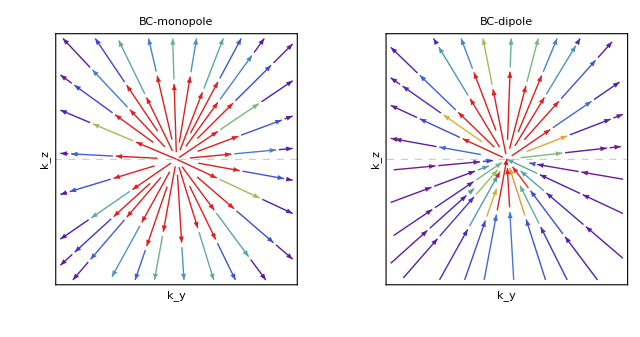

```mathematica
lim=π;limi=2;
p1=StreamPlot[kz{ky/((ky^2+kz^2)^2),kz/((ky^2+kz^2)^2)},{ky,-lim,lim},{kz,-limi,limi},StreamColorFunctionScaling->False,StreamColorFunction->"Rainbow",StreamStyle->Thick,StreamScale->0.18,StreamPoints->30,(**)Frame->True,FrameTicks->None,FrameTicksStyle->Directive[Bold,Gray,16],LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_y","k_z"},ImageSize->450,PlotLabel->Style[(****)"BC-dipole",20,FontFamily->"TexMaths Roman",Brown,Bold](**),GridLines->{None,{0}},GridLinesStyle->Directive[Lighter[Gray], Dashed,Thick]];

p2=StreamPlot[{ky/((ky^2+kz^2)^2),kz/((ky^2+kz^2)^2)},{ky,-lim,lim},{kz,-limi,limi},StreamColorFunctionScaling->False,StreamColorFunction->"Rainbow",StreamStyle->Thick,StreamScale->0.18,StreamPoints->30,(**)Frame->True,FrameTicks->None,LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_y","k_z"},ImageSize->450,PlotLabel->Style[(****)"BC-monopole",20,FontFamily->"TexMaths Roman",Brown,Bold],GridLines->{None,{0}},GridLinesStyle->Directive[Lighter[Gray], Dashed,Thick]];
plt=GraphicsRow[{p2,p1}]
Clear[kx];
SetDirectory[NotebookDirectory[]];
Export["dipole.pdf",Rasterize[plt],ImageResolution->100];
```

```mathematica
kz=0;lim=π;
StreamPlot[kz{ky/((kx^2+ky^2+kz^2)^2),kx/((kx^2+ky^2+kz^2)^2)},{ky,-lim,lim},{kx,-2,2},StreamColorFunctionScaling->False,StreamColorFunction->"Rainbow",StreamStyle->Thick,StreamScale->0.18,StreamPoints->30,(**)Frame->True,FrameTicks->None,FrameTicksStyle->Directive[Bold,Gray,16],LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_y","k_z"},ImageSize->450,PlotLabel->Style[(****)"BC-dipole",20,FontFamily->"TexMaths Roman",Brown,Bold](**),GridLines->{None,{0}},GridLinesStyle->Directive[Lighter[Gray], Dashed,Thick]]
Clear[kx,kz];
```